## Exclusion Plots, Run ~/Dropbox/nEDM/NStar/mNStar/mBpSens_2012.nb

## Initialize

```mathematica
OS="win";(*or,linux*)
(*SetOptions[$FrontEndSession,NotebookAutoSave->True]*)
NotebookSave[]
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c_old.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]]
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};

(***)
Print["oILL {Volume (m^3), Surface Area (m^2) = { ", voloill=Pi*(.24)^2*.12," , ",saoill=(2*Pi*(.24)^2)+(2Pi*.12*.24)," } "];
Print["NStar {Volume (m^3), Surface Area (m^2) = { ", voloill=Pi*(.24)^2*.12," , ",saoill=(2*Pi*(.24)^2)+(2Pi*.12*.24)," } "];
oillr=.24;oillh=.12;
Print["oILL {Volume (m^3), Surface Area (m^2) = { ", voloill=Pi*(oillr)^2*oillh," , ",saoill=(2*Pi*(oillr)^2)+(2Pi*oillr*oillh)," } "];
newr=1.4;newh=3.5;
Print["Diameter (1.14m) < ", N[Sqrt[(2newr)^2+newh^2]]];
Print["NStar_Capsule {Volume (m^3), Surface Area (m^2) = { ", volnew=N[10Pi newr^2/3]," , ",sanew=N[8Pi*newr^2]," } "];
Print["4V/A {oILL, NStar} (m) = { ",4voloill/saoill," , ",4volnew/sanew," } "];
vavg=3;
Print["t_f (s) { oILL , NStar } = { ",tfoill=4voloill/(vavg*saoill)," , ",tfnew=4volnew/(vavg*sanew)," } "];
tfil=11.5;illtau=12;fil=60;emp=60;oill=12;
nnn[tso_]:=2*(19268Exp[-tso/66]+14058Exp[-tso/326]);
fac[tso_,tco_]:=N[oill*(Sqrt[tso Sqrt[2*(19268Exp[-tso/66]+14058Exp[-tso/326])*(tco)]]/Sqrt[175Sqrt[17000*16*2]])];
hc=6.6×10^(-34)/(2Pi);mun=1.91304272*9.6623647*10^(−27);
taubp[bb_,bp_,tso_,beta_,nco_]:=((hc×8×(1.4275×10^6)*nco)/(mun*32))√(2/tfoill*(√(32/(nnn[tso]×nco)))^-1*(bb^2+bp^2+(2bp bb Cos[beta]))/((bp^2-bb^2)^2));
(***)
taue[bp_,bb_,m_]:=m/4 √(bb^2/(2 bp^2)Abs[(3 bp^2-bb^2)/((bb^2-bp^2)^2)])    
taubca[bp_,bb_,m_]:=m/4 √((bp bb)/((bb^2-bp^2)^2)) 
tauold[bb_,bp_,m_]:=m √((bb^2 (bb^2+bp^2+(2bp bb)))/((bp^2-bb^2)^2))
taubr[bp_,bb_,m_]:=m/4 √(bp/(2 bb(bb^2-bp^2))) ;
(**OLD**)
taubppnpi[bb_,bp_,tso_,beta_,nco_,tfoil_]:=((hc×8×(1.4275×10^6)*nco)/(mun*32))√(2/tfoil*(√(32/(nnn[tso]×nco)))^-1*(bb^2+bp^2+(2bp bb Cos[beta]))/((bp^2-bb^2)^2));
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

36

oILL {Volume (m^3), Surface Area (m^2) = { 0.0217147 , 0.542867 }

NStar {Volume (m^3), Surface Area (m^2) = { 0.0217147 , 0.542867 }

oILL {Volume (m^3), Surface Area (m^2) = { 0.0217147 , 0.542867 }

Diameter (1.14m) < 4.48219

NStar_Capsule {Volume (m^3), Surface Area (m^2) = { 20.5251 , 49.2602 }

4V/A {oILL, NStar} (m) = { 0.16 , 1.66667 }

t_f (s) { oILL , NStar } = { 0.0533333 , 0.555556 }

## Factor Change to accommodate lack of uncertainty of energy uncertainty

```mathematica
Print["Rati between <t_f> without energy uncertainty:with energy uncertainity, for 180s storage: ",((0.0033674/0.0610227))/((.0005/0.05430))];
Print["Rati between <t_f> without energy uncertainty:with energy uncertainity, for 180s storage, only uncertainities: ",((0.0033674))/((.0005))];
ninety95=1.96/1.64;
tffac=((0.0033674))/((.0005));
tffac^.25
tffac^.25*379
(tffac^.25)^.25*379
```

Rati between <t_f> without energy uncertainty:with energy uncertainity, for 180s storage: 5.99285

Rati between <t_f> without energy uncertainty:with energy uncertainity, for 180s storage, only uncertainities: 6.7348

1.61095

610.549

426.982

```mathematica
(*ω (<t_f>-1.96Sigma) < 1 *)
tf1=0.0739093+1.96*0.00401555
ω=2Pi/tf1;
γ=1.8*10^2; (*in Hz/μΤ*)
Print["B < ",bp=ω/(γ)]
Print["B (95% C.L.) < ",bp/1.96]
```

0.0817798

B < 0.426836

B (95% C.L.) < 0.217774

```mathematica
(*ω' (<t_f>-1.96Sigma) > 1 *)
tf2=(*0.0610227-1.96*0.00336746*)0.0502391-1.96*0.00239672
ω=2Pi/tf2;
γ=1.8*10^2; (*in Hz/μΤ*)
Print["B' > ",bp=ω/(γ)]
Print["B' (95% C.L.) > ",bp*1.96]
```

0.0455415

B' > 0.766478

B' (95% C.L.) > 1.5023

```mathematica
(*ω' (<t_f>-1.96Sigma) > 1 : Ramsey*)
tf3=0.0610227-1.96*0.00336746
ω=2Pi/tf3;
γ=1.8*10^2; (*in Hz/μΤ*)
Print["B'-nEDM > ",bp=ω/(γ)]
Print["B'-nEDM (95% C.L.) > ",bp*1.96]
```

0.0544225

B'-nEDM > 0.6414

B'-nEDM (95% C.L.) > 1.25714

```mathematica
(*For Ramsey type measurement*)
wup=PlusMinus[3.8424583,0.0000026]
wdown=PlusMinus[ 3.8424562,0.0000030]
wrasym=2(wup-wdown)/(wup+wdown)
```

3.84246±2.6×10^-6

3.84246±3.×10^-6

5.×10^-7±1.×10^-6

## Ratios

```mathematica
a10=e10=a20=e20={};
b10=b20={};
tstf10=tstf20={};
tstf102=tstf202={};
tsadd=PlusMinus[11.306,0.397];
For[i=1,i≤dimdesc,i++,
If[(*!MemberQ[{6,7,8,9,10,11,12,13,15,17,21,22,23,24,25,27,28,29,30,32,33,37},i]*)(descdat[[i]][[5]]>100&&descdat[[i]][[5]]<1000),
Print[descdat[[i]][[4]]];
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
If[descdat[[i]][[6]]==10,
a10=AppendTo[a10,PlusMinus[lvl3[[1]][[1]],lvl3[[1]][[2]]]];
e10=AppendTo[e10,PlusMinus[lvl3[[1]][[3]],lvl3[[1]][[4]]]];
b10=AppendTo[b10,PlusMinus[lvl3[[1]][[7]],lvl3[[1]][[8]]]];
tstf10=AppendTo[tstf10,(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]]];
tstf102=AppendTo[tstf102,(PlusMinus[descdat[[i]][[7]],.1]+tsadd)*PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]]];,
a20=AppendTo[a20,PlusMinus[lvl3[[1]][[1]],lvl3[[1]][[2]]]];
e20=AppendTo[e20,PlusMinus[lvl3[[1]][[3]],lvl3[[1]][[4]]]];
b20=AppendTo[b20,PlusMinus[lvl3[[1]][[7]],lvl3[[1]][[8]]]];
tstf20=AppendTo[tstf20,(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]]];
tstf202=AppendTo[tstf202,(PlusMinus[descdat[[i]][[7]],.1]+tsadd)*PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]]];
];
];
]
Print["<A_10> = ",Mean[a10]]
Quiet[Print["<A_10> 99% = ",a1099=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<A_10> 95% = ",a1095=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<A_10> 90% = ",a1090=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[a10][[2]]],x],{x,-10,0}],y][[1]])]]
(***)
Print["<E_10> = ",Mean[e10]]
Quiet[Print["<E_10> 99% = ",e1099=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<E_10> 95% = ",e1095=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<E_10> 90% = ",e1090=
(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,y}]==
0.1Integrate[ PDF[NormalDistribution[Mean[a10][[1]],Mean[e10][[2]]],x],{x,-10,0}],y][[1]])]]
(***)
Print["<B_10> = ",Mean[b10]]
(***)
Print["<A_20> = ",Mean[a20]]
Quiet[Print["<A_20> 99% = ",a2099=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<A_20> 95% = ",a2095=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<A_10> 90% = ",a2090=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[Mean[a20][[1]],Mean[a20][[2]]],x],{x,-10,0}],y][[1]])]]
(***)
Print["<E_20> = ",Mean[e20]]
Quiet[Print["<E_20> 99% = ",e2099=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<E_20> 95% = ",e2095=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,0}],y][[1]])]]
Quiet[Print["<E_20> 90% = ",e2090=(y/.Solve[Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[Mean[e20][[1]],Mean[e20][[2]]],x],{x,-10,0}],y][[1]])]]
(***)
Print["<B_20> = ",Mean[b20]]
Print["E_B0 < 99% = ",b0e99=1/Sqrt[(1/e1099)^2+(1/e2099)^2]]
Print["E_B0 < 95% = ",b0e95=1/Sqrt[(1/e1095)^2+(1/e2095)^2]]
Print["E_B0 < 90% = ",b0e90=1/Sqrt[(1/e1090)^2+(1/e2090)^2]]
Sqrt[400*.09/b0e90]
```

12693

12695

12697

12704

12707

13099

13142

13146

<A_10> = 0.00028±0.00028

<A_10> 99% = -0.000546126

<A_10> 95% = -0.000395358

<A_10> 90% = -0.000321379

<E_10> = -0.00008±0.0004

<E_10> 99% = -0.000847017

<E_10> 95% = -0.000621599

<E_10> 90% = -0.000509561

<B_10> = 0.0101954±1.5×10^-6

<A_20> = 0.0001±0.0004

<A_20> 99% = -0.000960392

<A_20> 95% = -0.000720966

<A_10> 90% = -0.000599675

<E_20> = 0.00043±0.00053

<E_20> 99% = -0.00108838

<E_20> 95% = -0.000794579

<E_20> 90% = -0.00064925

<B_20> = 0.0203867±1.×10^-7

E_B0 < 99% = 0.000668446

E_B0 < 95% = 0.000489585

E_B0 < 90% = 0.000400846

299.683

## B,(E-1)

```mathematica
gamman90=10^(-4)/(2Pi(29.1646943-1.64 0.0000069)) (*Gauss Units: 1Gauss = 10^-4T*)
gamman95=10^(-4)/(2Pi (29.1646943-1.96 0.0000069))
gamman99=10^(-4)/(2Pi (29.1646943-2.58 0.0000069))
dim10=Dimensions[e10][[1]]
dim20=Dimensions[e20][[1]]
taue1090=taue1095=taue1099={};
taue2090=taue2095=taue2099={};
tauo1090=tauo1095=tauo1099={};
tauo2090=tauo2095=tauo2099={};
taua1090=taua1095=taua1099={};
taua2090=taua2095=taua2099={};
For[i=1,i≤dim10,i++,
(*90*)
taue1090=
AppendTo[taue1090,Sqrt[(tstf10[[i]][[1]]*gamman90^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
taue1095=
AppendTo[taue1095,Sqrt[(tstf10[[i]][[1]]*gamman95^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
taue1099=
AppendTo[taue1099,Sqrt[(tstf10[[i]][[1]]*gamman99^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(*20*)
For[i=1,i≤dim20,i++,
(*90*)
taue2090=AppendTo[taue2090,Sqrt[(tstf20[[i]][[1]]*gamman90^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
taue2095=
AppendTo[taue2095,Sqrt[(tstf20[[i]][[1]]*gamman95^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
taue2099=
AppendTo[taue2099,Sqrt[(tstf20[[i]][[1]]*gamman99^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(***A***)
dim10=Dimensions[a10][[1]];
dim20=Dimensions[a20][[1]];
For[i=1,i≤dim10,i++,
(*90*)
taua1090=
AppendTo[taua1090,Sqrt[(tstf10[[i]][[1]]*gamman90^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a10[[i]][[1]]],a10[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
taua1095=
AppendTo[taua1095,Sqrt[(tstf10[[i]][[1]]*gamman95^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a10[[i]][[1]]],a10[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
taua1099=
AppendTo[taua1099,Sqrt[(tstf10[[i]][[1]]*gamman99^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a10[[i]][[1]]],a10[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(*20*)
For[i=1,i≤dim20,i++,
(*90*)
taua2090=AppendTo[taua2090,Sqrt[(tstf20[[i]][[1]]*gamman90^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a20[[i]][[1]]],a20[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
taua2095=
AppendTo[taua2095,Sqrt[(tstf20[[i]][[1]]*gamman95^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a20[[i]][[1]]],a20[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
taua2099=
AppendTo[taua2099,Sqrt[(tstf20[[i]][[1]]*gamman99^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[a20[[i]][[1]]],a20[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(***O***)
dim10=Dimensions[e10][[1]];
dim20=Dimensions[e20][[1]];
For[i=1,i≤dim10,i++,
(*90*)
tauo1090=
AppendTo[tauo1090,Sqrt[(tstf10[[i]][[1]]*gamman90^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
tauo1095=
AppendTo[tauo1095,Sqrt[(tstf10[[i]][[1]]*gamman95^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
tauo1099=
AppendTo[tauo1099,Sqrt[(tstf10[[i]][[1]]*gamman99^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e10[[i]][[1]]],e10[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e10[[i]][[1]],e10[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(*20*)
For[i=1,i≤dim20,i++,
(*90*)
tauo2090=AppendTo[tauo2090,Sqrt[(tstf20[[i]][[1]]*gamman90^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*95*)
tauo2095=
AppendTo[tauo2095,Sqrt[(tstf20[[i]][[1]]*gamman95^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
(*99*)
tauo2099=
AppendTo[tauo2099,Sqrt[(tstf20[[i]][[1]]*gamman99^2)/(Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[e20[[i]][[1]]],e20[[i]][[2]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[e20[[i]][[1]],e20[[i]][[2]]],x],{x,-10,0}],y][[1]])]])]];
];
(*A.Cos*)
mac=ReadList[StringJoin[descDir,seperator,"all_lvl3sidereal.dat"],{Word,Real,Real,Real,Real}];
(*90*)
mac1090r=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[1]][[2]]],Abs[mac[[1]][[3]]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[mac[[1]][[2]],Abs[mac[[1]][[3]]]],x],{x,-10,0}],y][[1]])]];
mac1090p=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[4]][[2]]],Abs[mac[[4]][[3]]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[mac[[4]][[2]],Abs[mac[[4]][[3]]]],x],{x,-10,0}],y][[1]])]];
(*95*)
mac1095r=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[1]][[2]]],Abs[mac[[1]][[3]]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[mac[[1]][[2]],Abs[mac[[1]][[3]]]],x],{x,-10,0}],y][[1]])]];
mac1095p=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[4]][[2]]],Abs[mac[[4]][[3]]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[mac[[4]][[2]],Abs[mac[[4]][[3]]]],x],{x,-10,0}],y][[1]])]];
(*99*)
mac1099r=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[1]][[2]]],Abs[mac[[1]][[3]]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[mac[[1]][[2]],Abs[mac[[1]][[3]]]],x],{x,-10,0}],y][[1]])]];
mac1099p=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[4]][[2]]],Abs[mac[[4]][[3]]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[mac[[4]][[2]],Abs[mac[[4]][[3]]]],x],{x,-10,0}],y][[1]])]];

(*20MuT*)
mac2090r=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[1]][[4]]],Abs[mac[[1]][[5]]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[mac[[1]][[4]],Abs[mac[[1]][[5]]]],x],{x,-10,0}],y][[1]])]];
mac2090p=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[4]][[4]]],Abs[mac[[4]][[5]]]],x],{x,-10,y}]==0.1Integrate[ PDF[NormalDistribution[mac[[4]][[4]],Abs[mac[[4]][[5]]]],x],{x,-10,0}],y][[1]])]];
(*95*)
mac2095r=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[1]][[4]]],Abs[mac[[1]][[5]]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[mac[[1]][[4]],Abs[mac[[1]][[5]]]],x],{x,-10,0}],y][[1]])]];
mac2095p=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[4]][[4]]],Abs[mac[[4]][[5]]]],x],{x,-10,y}]==0.05Integrate[ PDF[NormalDistribution[mac[[4]][[4]],Abs[mac[[4]][[5]]]],x],{x,-10,0}],y][[1]])]];
(*99*)
mac2099r=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[1]][[4]]],Abs[mac[[1]][[5]]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[mac[[1]][[4]],Abs[mac[[1]][[5]]]],x],{x,-10,0}],y][[1]])]];
mac2099p=Quiet[Abs[(y/.Solve[Integrate[ PDF[NormalDistribution[Abs[mac[[4]][[4]]],Abs[mac[[4]][[5]]]],x],{x,-10,y}]==0.01Integrate[ PDF[NormalDistribution[mac[[4]][[5]],Abs[mac[[4]][[5]]]],x],{x,-10,0}],y][[1]])]];
(**)
me1090=(Total[taue1090^4])^.25;Mean[taue1090]-1.64StandardDeviation[taue1090] ;
me1095=ninety95*((tffac^.25)*Total[taue1095^4])^.25;Mean[taue1095]-1.96 StandardDeviation[taue1095]; 
me1095o=(Total[taue1095^4])^.25;Mean[taue1095]-1.96 StandardDeviation[taue1095]; 
me1099=(Total[taue1099^4])^.25;Mean[taue1099]-2.58 StandardDeviation[taue1099] ;
me2090=(Total[taue2090^4])^.25;Mean[taue2090]-1.64StandardDeviation[taue2090] ;
me2095=ninety95*((tffac^.25)*Total[taue2095^4])^.25;Mean[taue2095]-1.96 StandardDeviation[taue2095] ;
me2095o=(Total[taue2095^4])^.25;Mean[taue2095]-1.96 StandardDeviation[taue2095] ;
me2099=(Total[taue2099^4])^.25;Mean[taue2099]-2.58 StandardDeviation[taue2099] ;
(*A.Cos*)
mac1090=10^3*Sqrt[Abs[Cos[2 Pi mac1090p]]/mac1090r]*gamman90; (*10^3 since the ampitudes were in ppm*)
mac1095=ninety95*((tffac^.25))^.25*10^3* Sqrt[Abs[Cos[2 Pi mac1095p]]/ mac1095r]*gamman95 ;
mac1095o=10^3* Sqrt[Abs[Cos[2 Pi mac1095p]]/ mac1095r]*gamman95 ;
mac1099=10^3*Sqrt[Abs[Cos[2 Pi mac1099p]]/mac1099r]*gamman99;
mac2090=10^3*300 Sqrt[Abs[Cos[2 Pi mac2090p]]/mac2090r]*gamman90 ;
mac2095=ninety95*((tffac^.25))^.25*10^3*Sqrt[Abs[Cos[2 Pi mac2095p]] /mac2095r]*gamman95 ;
mac2095o=10^3*Sqrt[Abs[Cos[2 Pi mac2095p]] /mac2095r]*gamman95 ;
mac2099=10^3*Sqrt[Abs[Cos[2 Pi mac2099p]]/mac2099r]*gamman99;
(*o*)
mo1090=(Total[tauo1090^4])^.25;Mean[tauo1090]-1.64StandardDeviation[tauo1090] ;
mo1095=ninety95*(tffac^.25*Total[tauo1095^4])^.25;Mean[tauo1095]-1.96 StandardDeviation[tauo1095]; 
mo1095o=(Total[tauo1095^4])^.25;Mean[tauo1095]-1.96 StandardDeviation[tauo1095]; 
mo1099=(Total[tauo1099^4])^.25;Mean[tauo1099]-2.58 StandardDeviation[tauo1099] ;
mo2090=(Total[tauo2090^4])^.25;Mean[tauo2090]-1.64StandardDeviation[tauo2090] ;
mo2095=ninety95*(tffac^.25*Total[tauo2095^4])^.25;Mean[tauo2095]-1.96 StandardDeviation[tauo2095] ;
mo2095o=(Total[tauo2095^4])^.25;Mean[tauo2095]-1.96 StandardDeviation[tauo2095] ;
mo2099=(Total[tauo2099^4])^.25;Mean[tauo2099]-2.58 StandardDeviation[tauo2099] ;
(*e*)
ma1090=(Total[taua1090^4])^.25;Mean[taua1090]-1.64StandardDeviation[taua1090] ;
ma1095=ninety95*(tffac^.25*Total[taua1095^4])^.25;Mean[taua1095]-1.96 StandardDeviation[taua1095]; 
ma1095o=(Total[taua1095^4])^.25;Mean[taua1095]-1.96 StandardDeviation[taua1095]; 
ma1099=(Total[taua1099^4])^.25;Mean[taua1099]-2.58 StandardDeviation[taua1099] ;
ma2090=(Total[taua2090^4])^.25;Mean[taua2090]-1.64StandardDeviation[taua2090] ;
ma2095=ninety95*(tffac^.25*Total[taua2095^4])^.25;Mean[taua2095]-1.96 StandardDeviation[taua2095] ;
ma2095o=(Total[taua2095^4])^.25;Mean[taua2095]-1.96 StandardDeviation[taua2095] ;
ma2099=(Total[taua2099^4])^.25;Mean[taua2099]-2.58 StandardDeviation[taua2099] ;
(********************************)
Print["E"];
taue[1*10^(-6),(Mean[b10][[1]]-1.64Mean[b10][[2]])*.001,me1090]
taue[1*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*.001,me1095]
taue[1*10^(-6),(Mean[b10][[1]]-2.58Mean[b10][[2]])*.001,me1099]
taue[1*10^(-6),(Mean[b20][[1]]-1.64Mean[b20][[2]])*.001,me2090]
taue[1*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*.001,me2095]
taue[1*10^(-6),(Mean[b20][[1]]-2.58Mean[b20][[2]])*.001,me2099]
Print["O"];
tauold[1*10^(-6),(Mean[b10][[1]]-1.64Mean[b10][[2]])*.001,mo1090]
tauold[1*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*.001,mo1095]
tauold[1*10^(-6),(Mean[b10][[1]]-2.58Mean[b10][[2]])*.001,mo1099]
tauold[1*10^(-6),(Mean[b20][[1]]-1.64Mean[b20][[2]])*.001,mo2090]
tauold[1*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*.001,mo2095]
tauold[1*10^(-6),(Mean[b20][[1]]-2.58Mean[b20][[2]])*.001,mo2099]
Print["A"];
taubca[1*10^(-6),(Mean[b10][[1]]-1.64Mean[b10][[2]])*.001,ma1090]
taubca[1*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*.001,ma1095]
taubca[1*10^(-6),(Mean[b10][[1]]-2.58Mean[b10][[2]])*.001,ma1099]
taubca[1*10^(-6),(Mean[b20][[1]]-1.64Mean[b20][[2]])*.001,ma2090]
taubca[1*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*.001,ma2095]
taubca[1*10^(-6),(Mean[b20][[1]]-2.58Mean[b20][[2]])*.001,ma2099]
Print["A.Cos"];
taubca[1*10^(-6),(Mean[b10][[1]]-1.64Mean[b10][[2]])*.001,mac1090]
taubca[1*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*.001,mac1095]
taubca[1*10^(-6),(Mean[b10][[1]]-2.58Mean[b10][[2]])*.001,mac1099]
taubca[1*10^(-6),(Mean[b20][[1]]-1.64Mean[b10][[2]])*.001,mac2090]
taubca[1*10^(-6),(Mean[b20][[1]]-1.96Mean[b10][[2]])*.001,mac2095]
taubca[1*10^(-6),(Mean[b20][[1]]-2.58Mean[b10][[2]])*.001,mac2099]
```

5.45711×10^-7

5.45711×10^-7

5.45711×10^-7

5

3

E

426.026

390.572

214.3

320.236

333.768

190.894

O

0.000263462

0.00024155

0.000132548

0.0000935558

0.0000975094

0.0000557693

A

26.2861

34.0546

12.7536

8.42375

6.97997

3.60604

A.Cos

8.04007

9.16883

2.61149

388.954

1.86629

1.25181

E_B, τ: {44.1124,{0.6414→6.10103}}

A_B, τ: {83.0704,{0.6414→16.3417}}

A_B, τ @ 100μT: 3.31064

A_B-cos, τ: {22.3016,{0.6414→16.3554}}

E_B-B limits: Solve[False,0.6414]

A_B-B limits: Solve[False,0.6414]

A_BCos-B limits: Solve[False,0.6414]

0.275611 √(bb^2) m √Abs[(1.23418-bb^2)/((-0.411394+bb^2)^2)]

0.200219 √(bb/((-0.411394+bb^2)^2)) m

0.6414 √((0.411394+1.2828 bb+bb^2)/((-0.411394+bb^2)^2)) m

(***)

(√(11/2))/240

(√(5/2))/198

1/9

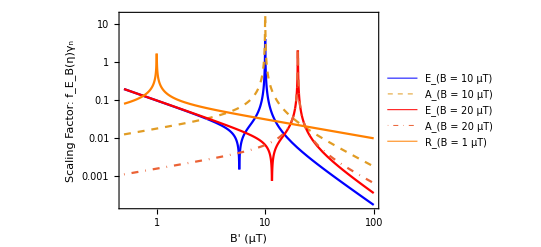

-Graphics-

```mathematica
mincur=FindMinimum[ ((taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),me1095]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),me2095]^4)/2)^0.25,{bp,9,50}];
Print["E_B, τ: ",mincur]
mincuraa=FindMinimum[ ((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),ma1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),ma2095]^4)/2)^0.25,{bp,11,19}];
Print["A_B, τ: ",mincuraa]
Print["A_B, τ @ 100μT: ",((taubca[100*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),ma1095]^4)/2+(taubca[100*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),ma2095]^4)/2)^0.25]
mincuraa2=FindMinimum[ ((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),mac1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),mac2095]^4)/2)^0.25,{bp,11,19}];
Print["A_B-cos, τ: ",mincuraa2]
(*B-limitss*)
Quiet[
Print["E_B-B limits: ",
Solve[((taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),me1095]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),me2095]^4)/2)^0.25==mincur[[1]],bp]];
Print["A_B-B limits: ",
Solve[((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),ma1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),ma2095]^4)/2)^0.25==mincuraa[[1]],bp]];
Print["A_BCos-B limits: ",
Solve[((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),mac1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),mac2095]^4)/2)^0.25==mincuraa2[[1]],bp]];
]
(**)
taue[bp,bb,m]
taubca[bp,bb,m]
tauold[bp,bb,m]
Print["(***)"]
Sqrt[taue[20,10,1]^2]
taubca[1,10,1]
tauold[1,10,1]
LogLogPlot[{
gamman95*taue[bp*10^(-6),10*10^(-6),1],
gamman95*taubca[bp*10^(-6),10*10^(-6),1]4,
gamman95*taue[bp*10^(-6),20*10^(-6),1],
gamman95*taubca[bp*10^(-6),20*10^(-6),1],
gamman95*(taubr[bp*10^(-6),1*10^(-6),1]^4)^.25},{bp,.5,100},
PlotLegends->{"E_(B = 10  μT)","A_(B = 10  μT)","E_(B = 20  μT)","A_(B = 20  μT)","R_(B = 1  μT)"},PlotStyle->{{Thickness[.004],Blue},{Thickness[.004],Dashed},{Thickness[.004],Red},{Thickness[.004],DotDashed},{Thickness[.004],Orange}},Frame->True,FrameLabel->{"B' (μT)","Scaling Factor: f_E_B(η)γ_n"},FrameTicks->{LogTicks,None,LogTicks,None},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200}]
Plot[fzba[x],{x,0,100}]
```

## Read ZB’s list

```mathematica
zbdata=ReadList[StringJoin[descDir,seperator,"Listb_zb.dat"],{Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real}];
dimzbdata=Dimensions[zbdata][[1]];
(*A*)
ptzbaglobal=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[13]]*2/1.96},{k,1,dimzbdata}];(*2018_ZB_GlobalConstraint*)
ftzbaglobal=Interpolation[ptzbaglobal];
ptzba1=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[2]]*2/1.96},{k,1,dimzbdata}];(*Altarev*)
ftzba1=Interpolation[ptzba1];
ptzba2u=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[4]]*1.645/2},{k,1,dimzbdata}];(*Ban_Upper*)
ftzba2u=Interpolation[ptzba2u];
ptzba2l=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[5]]*1.645/2},{k,1,dimzbdata}];(*Ban_Lower*)
ftzba2l=Interpolation[ptzba2l];
ptzba3u=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[8]]*2/1.96},{k,1,dimzbdata}];(*Serebrov_Upper-From_2012_ZB*)
ftzba3u=Interpolation[ptzba3u];
ptzba3l=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[9]]*2/1.96},{k,1,dimzbdata}];(*Serebrov_Lower-From_2012_ZB*)
ftzba3l=Interpolation[ptzba3l];
(*fzba=Interpolation[ptzba];(*A*)*)
(*fzbe=Interpolation[ptzbe];(*E*)*)
(*E*)
ptzbeglobal=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[12]]},{k,1,dimzbdata}];(*2018_ZB_GlobalConstraint*)
ftzbeglobal=Interpolation[ptzbeglobal];
ptzbe1=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[3]]*2/1.96},{k,1,dimzbdata}];(*Altarev*)
ftzbe1=Interpolation[ptzbe1];
ptzbe2=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[6]]*2/1.96},{k,1,dimzbdata}];(*Ban*)
ftzbe2=Interpolation[ptzbe2];
ptzbe3=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[7]]*2.56/1.96},{k,1,dimzbdata}];(*Serebrov-448s-Horizontal, 95%*)
ftzbe3=Interpolation[ptzbe3];
ptzbe4u=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[10]]*1.645/2},{k,1,dimzbdata}];(*Serebrov-apparatus_upper, 2018_ZB_new_analysis%*)
ftzbe4u=Interpolation[ptzbe4u];
ptzbe4l=Table[{zbdata[[k]][[1]]*100,zbdata[[k]][[11]]*1.645/2},{k,1,dimzbdata}];(*Serebrov-apparatus_lower, 2018_ZB_reanalysis%*)
ftzbe4l=Interpolation[ptzbe4l];
```

InterpolatingFunction::dmval: Input value {99.874} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100.167} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100.456} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

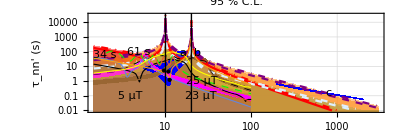

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\new_taubp_all_3.png

```mathematica
lineStyle={Thick,Black};
ln1=Line[{Log@{10.2,0.001},Log@{10.2,10^5}}];
ln2=Line[{Log@{20.4,0.001},Log@{20.4,10^5}}];
pnt3=Point[Log@{9.8,5.2}];
pnt4=Point[Log@{11,4.4}];
pnt5=Point[Log@{11.4,1.2}];
thk=.004;tfoill=0.05333333333333333;
(*These only create 10 powers*)
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l-N[Log10[2]],u+N[Log10[2]],int}]],3];
tk22[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[
Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,2]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,3]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,4]],u,int}]~Join~
Table[{10^j,"",{N[c],d}},{j,l+N[Log[10,5]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,6]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,7]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,8]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,9]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log[10,10]],u,int}]
],3];
tk23[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[
Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[2]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[3]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[4]],u,int}]~Join~
Table[{10^j,"",{N[c],d}},{j,l+N[Log10[5]],u,int}]
],3];
fixLogPlots[gr_]:=gr/.f:(Ticks|FrameTicks->_):>(f/._Thickness:>(##&[]));
exprt=LogLogPlot[
{
(*1*)ConditionalExpression[34,0<bp<25],
(*2*)ConditionalExpression[110,((14.2<bp<19.5))],
(*3*) ConditionalExpression[ ((bp-11.065)^2)+2,7<bp<11.59]/4,
(*4*)ConditionalExpression[-taubppnpi[0,bp,198,0,380,tfoill*CubeRoot[3]]+taubppnpi[20,bp,198,0,320,tfoill*CubeRoot[3]],((11.59<bp<19.375))],
(*5*)ConditionalExpression[taubppnpi[20,bp+5,198,0,380,tfoill*CubeRoot[3]],7<bp<14.2],
(*6*) ConditionalExpression[ Sqrt[2.3^2-(bp-8)^2]*1.7+7.09,1<bp<7],
(*7*)ConditionalExpression[ -Sqrt[2.3^2-(bp-8)^2]*1.7+8.09,1<bp<7],
(*8*)ConditionalExpression[taubppnpi[20,bp-5,198,0,256,tfoill*CubeRoot[3]],((25.45<bp<29.5))],
(*9*)ConditionalExpression[taubppnpi[20,bp,198,0,500,tfoill*CubeRoot[3]],((20.1<bp<10000))],
(*10*)ConditionalExpression[110,((20.9<bp<25.45))],
(*11*)ConditionalExpression[taubppnpi[56,bp,198,0,480,tfoill*CubeRoot[3]*1.7],((200<bp<340))],
(*12*)ConditionalExpression[(100/bp)+.005,((340<bp<2000))],
(*(*13*)Max[{taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),me1095],taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),me2095]}],*)
(*13*)(( taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),me1095o]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),me2095o]^4)/2)^0.25,
(*14*)(( taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),me1095]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),me2095]^4)/2)^0.25,
(*15*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),mac1095o]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),mac2095o]^4)/2)^0.25,
(*16*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),mac1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),mac2095]^4)/2)^0.25,
(*17*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),ma1095o]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),ma2095o]^4)/2)^0.25,
(*18*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*10^(-3),ma1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*10^(-3),ma2095]^4)/2)^0.25,
(*19*)ConditionalExpression[ftzbeglobal[bp],0.5<bp<100],
(*20*)ConditionalExpression[ftzbaglobal[bp],0.5<bp<100],
(*A*)
(*21*)ConditionalExpression[ftzba1[bp],0.5<bp<100],
(*22*)ConditionalExpression[ftzba2u[bp],0.5<bp<100],
(*23*)ConditionalExpression[ftzba2l[bp],0.5<bp<100],
(*NEW <B'_⇔>_min,<B'_⇕>_max*)
(*24*)ConditionalExpression[ftzba3u[bp],0.5<bp<100],
(*25*)ConditionalExpression[ftzba3l[bp],0.5<bp<100],
(*E*)
(*26*)ConditionalExpression[ftzbe1[bp],0.5<bp<100],
(*27*)ConditionalExpression[ftzbe2[bp],0.5<bp<100],
(*28*)ConditionalExpression[ftzbe3[bp],0.5<bp<100],
(*29*)ConditionalExpression[ftzbe4u[bp],0.5<bp<100],
(*30*)ConditionalExpression[ftzbe4l[bp],0.5<bp<100],
(*(*21*)Sqrt[.3^2-(bp-6)^2]*100+40,
(*22*)ConditionalExpression[taubppnpi[6,bp,198,0,380,tfoill]/7,((bp<5.7)||(bp>6.3))],
(*23*)ConditionalExpression[61,5<bp<23],*)
},{bp,1.5,3000},
PlotRange->{{1.5,3000},{.01,29999}},Axes->None,GridLines->Automatic,
Filling->{{1->0.001},{3->{{5},Blue}},{4->{{5},Blue}},{4->{{2},Blue}},{6->{{7},Blue}},{9->{{10},Blue}},{9->{{11},Blue}},{9->{{12},Blue}},
{13->{0.001,Directive[Opacity[.45],Red]}},
{14->{0.001,Directive[Opacity[.45],Red]}},
{15->{0.001,Directive[Opacity[.45],Cyan]}},
{16->{0.001,Directive[Opacity[.45],Cyan]}},
{17->{0.001,Directive[Opacity[.45],Orange]}},
{18->{0.001,Directive[Opacity[.45],Orange]}},
{19->0.001},
{20->0.001},
{21->0.001},
{22->{{23},Magenta}},
{24->{{25},Brown}},
{26->0.001},
{27->0.001},
{28->0.001},
{29->{30},Yellow}},
PlotStyle->{(*1*)None,(*2*)None,(*3*)None,(*4*)None,(*5*)None,(*6*)None,(*7*)None,(*8*)None,(*9*)None,(*10*)None,(*11*)None,(*12*)None,
(*13*){Red,Thickness[thk]},
(*14*){Red,Thickness[thk],DotDashed},
(*15*){LightBlue,Thickness[thk],Dashed},
(*16*){LightBlue,Thickness[thk],DotDashed},
(*17*){Purple,Thickness[thk],Dashed},
(*18*){Purple,Thickness[thk],DotDashed},
(*19*){Black,Thickness[thk/2]},
(*20*){Black,Thickness[thk/2],Dashed},
(*21*){Green,Thickness[thk/2],Dashed},
(*22*){Magenta,Thickness[thk/2],Dashed},
(*23*)None,
(*24*){Brown,Thickness[thk/2],Dashed},
(*25*)None,
(*26*){Automatic,Thickness[thk/2]},
(*27*){Automatic,Thickness[thk/2]},
(*28*){Automatic,Thickness[thk/2]},
(*29*){Yellow,Thickness[thk/2]},
(*30*)None
},Frame->True,FrameStyle->Thickness[thk],FrameTicks->{(*y,x*){tk22[-2,4,.02,0,0.015,0,1],tk22[-2,4,.02,0,0.015,0,1]},{tk22[-2,4,.02,0,0.015,0,1],tk22[-2,4,.02,0,0.015,0,1]}},FrameTicksStyle->{Directive[Black,Thickness[thk/2]],Directive[Black,Thickness[thk]]},FrameLabel->{"B' (μT)","τ_nn' (s)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
PlotLegends->Placed[LineLegend[Flatten[Join[Table["",{k,1,12}],{
(*13*)"This paper:E_B",
(*14*)"This paper [w/o σ-ρ(E)]:E_B",
(*15*)"This paper:Cos[β=Ωt]·A_B",
(*16*)"This paper [w/o σ-ρ(E)]:Cos[β=Ωt]·A_B",
(*17*)"This paper:A_B",
(*18*)"This paper [w/o σ-ρ(E)]:A_B",
(*19*)"ZB:E_B",
(*20*)"ZB:A_B",
(*21*)"Altarev:A_B",
(*22*)"Ban_(max, min):A_B",
(*23*)"",
(*24*)"APS_(max, min):A_B",
(*25*)"",
(*26*)"Altarev:E_B",
(*27*)"Ban:E_B",
(*28*)"APS_⇔:E_B",
(*29*)"APS-ZB_(max, min):E_B",
(*30*)""
}]],LegendLayout->{"Row",6}],Bottom],PlotLabel->"95 % C.L.",
Epilog->{
{Directive[{PointSize[.0075],Black}],pnt3,pnt4,pnt5},
{Directive[lineStyle],ln1,ln2,Text[Style["a",FontSize->Large],Log@{16,75}],Text[Style["b",FontSize->Large],Log@{24,75}],Text[Style["c",FontSize->Large],Log@{800,.15}],
Text[Style["34 s",FontSize->Large],Log@{2,55}],
Text[Style["25 μT",FontSize->Large],Log@{27,1}],
Text[Style["61 s",FontSize->Large],Log@{5,100}],
Text[Style["5 μT",FontSize->Large],Log@{4,.1}],
Text[Style["23 μT",FontSize->Large],Log@{26,.1}]}
},ImageSize->{1400},AspectRatio->1/3
]
Export[StringJoin[PicDir,seperator,"new_taubp_all_3.png"],exprt]
```

## Separate Plots

InterpolatingFunction::dmval: Input value {99.874} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100.167} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100.456} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

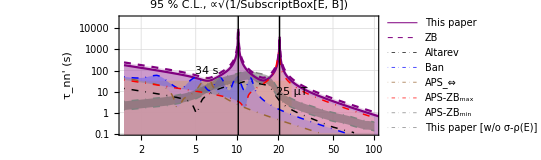

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\new_taubp_E_ppt-3.png

```mathematica
(*These create appropriate integers*)
tk3[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[
Table[{10^j,SetPrecision[10^j,3],{a,b}},{j,l,u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[2*int]],u,int}]
],3];
tk32[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[
Table[{10^j,SetPrecision[10^j,3],{a,b}},{j,l,u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[2*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[3*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[4*int]],u,int}]~Join~
Table[{10^j,"",{N[c],d}},{j,l+N[Log10[5*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[6*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[7*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[8*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[9*int]],u,int}]
],3];
exprt2=LogLogPlot[
{
(*1*)ConditionalExpression[33,0<bp<25],

(*2*)((taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,me1095o]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,me2095o]^4)/2)^0.25,
(*3*)((taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,me1095]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,me2095]^4)/2)^0.25,

(*4*)ConditionalExpression[ftzbeglobal[bp],0.2<bp<100],
(*E*)
(*5*)ConditionalExpression[ftzbe1[bp],0.2<bp<100],
(*6*)ConditionalExpression[ftzbe2[bp],0.2<bp<100],
(*7*)ConditionalExpression[ftzbe3[bp],0.2<bp<100],
(*8*)ConditionalExpression[ftzbe4u[bp],0.2<bp<100],
(*9*)ConditionalExpression[ftzbe4l[bp],0.2<bp<100]
},{bp,1.5,3000},
PlotRange->{{1.5,99},{.11,29999}},Axes->None,GridLines->Automatic,
Filling->{
{1->{0.001,Directive[Opacity[.45],Yellow]}},
{2->{0.001,Directive[Opacity[.45],Lighter[Purple]]}},
{3->{0.001,Directive[Opacity[.25],Lighter[Purple]]}},
{4->{0.001,Directive[Opacity[.45],Lighter[Gray]]}},
{5->{0.001,Directive[Opacity[.45],Lighter[Blue]]}},
{6->{0.001,Directive[Opacity[.45],Lighter[Brown]]}},
{7->{0.001,Directive[Opacity[.45],Lighter[Pink]]}},
{8->{{9},Directive[Opacity[.45],Darker[Gray]]}}
},
PlotStyle->{
(*1*)None,
(*2*){Purple,Thickness[thk]},
(*3*){Purple,Dashed,Thickness[thk]},
(*4*){Black,DotDashed,Thickness[2thk/3]},
(*5*){Blue,DotDashed,Thickness[2thk/3]},
(*6*){Brown,DotDashed,Thickness[2thk/3]},
(*7*){Red,DotDashed,Thickness[2thk/3]},
(*8*){Gray,DotDashed,Thickness[2thk/3]},
(*9*){Gray,DotDashed,Thickness[2thk/3]}
},Frame->True,FrameStyle->Thickness[thk],FrameTicks->{(*y,x*){tk22[-1,4,.02,0,0.015,0,1],tk22[-1,4,.02,0,0.015,0,1]},{tk3[-1,3,.02,0,0.015,0,1/4],tk22[-1,3,.02,0,0.015,0,1]}},FrameTicksStyle->{Directive[Black,Thickness[thk/2]],Directive[Black,Thickness[thk]]},FrameLabel->{"B' (μT)","τ_nn' (s)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
PlotLegends->Placed[LineLegend[Flatten[Join[Table["",{k,1,1}],{
"This paper",
(*16*)"ZB",
(*23*)"Altarev",
(*24*)"Ban",
(*25*)"APS_⇔",
(*26*)"APS-ZB_max",
(*26*)"APS-ZB_min",
"This paper [w/o σ-ρ(E)]",
}]],LegendLayout->{"Row",1}],Bottom],
PlotLabel->"95 % C.L., ∝√(1/SubscriptBox[E, B])",Epilog->{
{Directive[{PointSize[.0075],Black}](*,pnt3,pnt4,pnt5*)},
{Directive[lineStyle],ln1,ln2,
Text[Style["34 s",FontSize->Large],Log@{6,100}],
Text[Style["25 μT",FontSize->Large],Log@{25,10}],
(*Text[Style["7.8 s",FontSize->Large],Log@{1,5}],
Text[Style["15 μT",FontSize->Large],Log@{8,.1}],
Text[Style["28 μT",FontSize->Large],Log@{32,.1}]*)}
},
ImageSize->{1400},AspectRatio->1/2.5
]
Export[StringJoin[PicDir,seperator,"new_taubp_E_ppt-3.png"],exprt2]
```

InterpolatingFunction::dmval: Input value {99.874} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100.167} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100.456} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

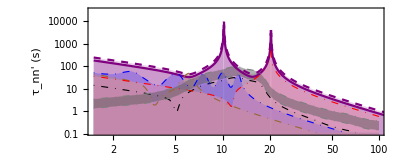

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\new_taubp_E_pr_APS-90cl_3.png

```mathematica
(*These create appropriate integers*)
tk3[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[
Table[{10^j,SetPrecision[10^j,3],{a,b}},{j,l,u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[2*int]],u,int}]
],3];
tk32[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[
Table[{10^j,SetPrecision[10^j,3],{a,b}},{j,l,u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[2*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[3*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[4*int]],u,int}]~Join~
Table[{10^j,"",{N[c],d}},{j,l+N[Log10[5*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[6*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[7*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[8*int]],u,int}]~Join~
Table[{10^j,"",{N[c/2],d}},{j,l+N[Log10[9*int]],u,int}]
],3];
exprt2b=LogLogPlot[
{
(*1*)ConditionalExpression[33,0<bp<25],

(*2*)((taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,me1095o]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,me2095o]^4)/2)^0.25,

(*3*)ConditionalExpression[ftzbeglobal[bp],0.2<bp<100],
(*E*)
(*4*)ConditionalExpression[ftzbe1[bp],0.2<bp<100],
(*5*)ConditionalExpression[ftzbe2[bp],0.2<bp<100],
(*6*)ConditionalExpression[ftzbe3[bp],0.2<bp<100],
(*7*)ConditionalExpression[ftzbe4u[bp],0.2<bp<100],
(*8*)ConditionalExpression[ftzbe4l[bp],0.2<bp<100],
(*9*)((taue[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,me1095]^4)/2+(taue[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,me2095]^4)/2)^0.25
},{bp,1.5,3000},
PlotRange->{{1.5,99},{.11,29999}},Axes->None,GridLines->Automatic,
Filling->{
None,
{2->{0.001,Directive[Opacity[.45],Lighter[Purple]]}},
{3->{0.001,Directive[Opacity[.45],Lighter[Gray]]}},
{4->{0.001,Directive[Opacity[.45],Lighter[Blue]]}},
{5->{0.001,Directive[Opacity[.45],Lighter[Brown]]}},
{6->{0.001,Directive[Opacity[.45],Lighter[Pink]]}},
{7->{{8},Directive[Opacity[.45],Darker[Gray]]}},
{9->{0.001,Directive[Opacity[.25],Lighter[Purple]]}}
},
PlotStyle->{
(*1*)None,
(*2*){Purple,Thickness[thk]},
(*3*){Black,DotDashed,Thickness[thk/2]},
(*4*){Blue,DotDashed,Thickness[thk/2]},
(*5*){Brown,DotDashed,Thickness[thk/2]},
(*6*){Red,DotDashed,Thickness[thk/2]},
(*7*){Gray,DotDashed,Thickness[thk/2]},
(*8*){Gray,DotDashed,Thickness[thk/2]},
(*9*){Purple,Dashed,Thickness[thk]}
},Frame->True,FrameStyle->Thickness[thk],FrameTicks->{(*y,x*){tk22[-1,4,.02,0,0.015,0,1],tk22[-1,4,.02,0,0.015,0,1]},{tk3[-1,3,.02,0,0.015,0,1/4],tk22[-1,3,.02,0,0.015,0,1]}},FrameTicksStyle->{Directive[Black,Thickness[thk/2]],Directive[Black,Thickness[thk]]},FrameLabel->{"B' (μT)","τ_nn' (s)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
ImageSize->{1400},AspectRatio->1/2.5
]
Export[StringJoin[PicDir,seperator,"new_taubp_E_pr_APS-90cl_3.png"],exprt2b]
```

InterpolatingFunction::dmval: Input value {104.272} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {107.687} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {109.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

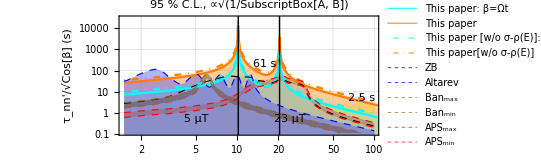

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\new_taubp_A_ppt_APS-90cl_3.png

```mathematica
exprt3=LogLogPlot[
{
(*1*)ConditionalExpression[2.5,.8<bp<100],
(*2*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,mac1095o]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,mac2095o]^4)/2)^0.25,
(*3*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095o]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095o]^4)/2)^0.25,
(*4*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,mac1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,mac2095]^4)/2)^0.25,
(*5*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095]^4)/2)^0.25,
(*6*)ConditionalExpression[ftzbaglobal[bp],0.2<bp<100],
(*A*)
(*7*)ConditionalExpression[ftzba1[bp],0.2<bp<100],
(*8*)ConditionalExpression[ftzba2u[bp],0.2<bp<100],
(*9*)ConditionalExpression[ftzba2l[bp],0.2<bp<100],
(*10*)ConditionalExpression[ftzba3u[bp],0.2<bp<100],
(*11*)ConditionalExpression[ftzba3l[bp],0.2<bp<100],
},{bp,1.5,3000},
PlotRange->{{1.5,99},{.11,29999}},Axes->None,GridLines->Automatic,
Filling->{
{1->{0.001,Directive[Opacity[.45],Yellow]}},
{2->{0.001,Directive[Opacity[.45],Lighter[Cyan]]}},
{3->{0.001,Directive[Opacity[.45],Lighter[Orange]]}},
{4->{0.001,Directive[Opacity[.25],Lighter[Cyan]]}},
{5->{0.001,Directive[Opacity[.25],Lighter[Orange]]}},
{6->{0.001,Directive[Opacity[.45],Lighter[Gray]]}},
{7->{0.001,Directive[Opacity[.45],Lighter[Blue]]}},
{8->{{9},Directive[Opacity[.45],Darker[Brown]]}},
{10->{{11},Directive[Opacity[.45],Darker[Pink]]}}
},PlotStyle->{
None,
(*2*){Cyan,Thickness[thk]},
(*3*){Orange,Thickness[thk]},
(*4*){Cyan,Thickness[thk],DotDashed},
(*5*){Orange,Thickness[thk],DotDashed},
(*6*){Black,Dashed,Thickness[thk/2]},
(*7*){Blue,Dashed,Thickness[thk/2]},
(*8*){Brown,Dashed,Thickness[thk/2]},
(*9*){Brown,Dashed,Thickness[thk/2]},
(*10*){Red,Dashed,Thickness[thk/2]},
(*11*){Red,Dashed,Thickness[thk/2]}
},Frame->True,FrameStyle->Thickness[thk],FrameTicks->{(*y,x*){tk22[-1,5,.02,0,0.015,0,1],tk22[-1,5,.02,0,0.015,0,1]},{tk3[-1,3,.02,0,0.015,0,1/4],tk22[-1,3,.02,0,0.015,0,1]}},FrameTicksStyle->{Directive[Black,Thickness[thk/2]],Directive[Black,Thickness[thk]]},FrameLabel->{"B' (μT)","τ_nn'/√Cos[β] (s)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},
PlotLegends->Placed[LineLegend[Flatten[Join[Table["",{k,1,1}],{
"This paper: β=Ωt",
"This paper",
"This paper [w/o σ-ρ(E)]: β=Ωt",
"This paper[w/o σ-ρ(E)]",
(*17*)"ZB",
(*18*)"Altarev",
(*19*)"Ban_max",
(*20*)"Ban_min",
(*21*)"APS_max",
(*22*)"APS_min"
}]],LegendLayout->{"Row",2}],Bottom],
PlotLabel->"95 % C.L., ∝√(1/SubscriptBox[A, B])",
Epilog->{
{Directive[{PointSize[.0075],Black}]},
{Directive[lineStyle],ln1,ln2,
Text[Style["2.5 s",FontSize->Large],Log@{80,5}],
(*Text[Style["25 μT",FontSize->Large],Log@{25,10}],*)
Text[Style["61 s",FontSize->Large],Log@{16,200}],
Text[Style["5 μT",FontSize->Large],Log@{5,.5}],
Text[Style["23 μT",FontSize->Large],Log@{24,.5}]}
},ImageSize->{1400},AspectRatio->1/2.5
]
Export[StringJoin[PicDir,seperator,"new_taubp_A_ppt_APS-90cl_3.png"],exprt3]
```

```mathematica
bpp=65;
((taubca[bpp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095o]^4)/2+(taubca[bpp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095o]^4)/2)^0.25/ftzbaglobal[bpp]
((taubca[bpp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095o]^4)/2+(taubca[bpp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095o]^4)/2)^0.25
ftzbaglobal[bpp]
```

9.86287

4.84262

0.490995

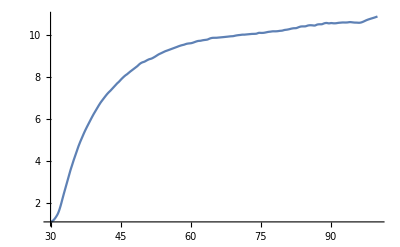

```mathematica
Plot[((taubca[bpp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095o]^4)/2+(taubca[bpp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095o]^4)/2)^0.25/ftzbaglobal[bpp],{bpp,30,100}]
```

InterpolatingFunction::dmval: Input value {104.272} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {107.687} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {109.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

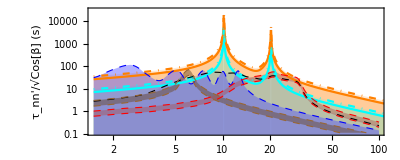

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\new_taubp_A_pr_APS-90cl_3.png

```mathematica
exprt3b=LogLogPlot[
{
(*1*)ConditionalExpression[2.5,.8<bp<100],
(*2*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,mac1095o]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,mac2095o]^4)/2)^0.25,
(*3*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095o]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095o]^4)/2)^0.25,
(*4*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,mac1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,mac2095]^4)/2)^0.25,
(*5*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095]^4)/2)^0.25,
(*6*)ConditionalExpression[ftzbaglobal[bp],0.2<bp<100],
(*A*)
(*7*)ConditionalExpression[ftzba1[bp],0.2<bp<100],
(*8*)ConditionalExpression[ftzba2u[bp],0.2<bp<100],
(*9*)ConditionalExpression[ftzba2l[bp],0.2<bp<100],
(*10*)ConditionalExpression[ftzba3u[bp],0.2<bp<100],
(*11*)ConditionalExpression[ftzba3l[bp],0.2<bp<100]
},{bp,1.5,3000},
PlotRange->{{1.5,99},{.11,29999}},Axes->None,GridLines->Automatic,
Filling->{
None,
{2->{0.001,Directive[Opacity[.45],Lighter[Cyan]]}},
{3->{0.001,Directive[Opacity[.45],Lighter[Orange]]}},
{4->{0.001,Directive[Opacity[.25],Lighter[Cyan]]}},
{5->{0.001,Directive[Opacity[.25],Lighter[Orange]]}},
{6->{0.001,Directive[Opacity[.45],Lighter[Gray]]}},
{7->{0.001,Directive[Opacity[.45],Lighter[Blue]]}},
{8->{{9},Directive[Opacity[.45],Darker[Brown]]}},
{10->{{11},Directive[Opacity[.45],Darker[Pink]]}}
},PlotStyle->{
None,
(*2*){Cyan,Thickness[thk]},
(*3*){Orange,Thickness[thk]},
(*4*){Cyan,Thickness[thk],DotDashed},
(*5*){Orange,Thickness[thk],DotDashed},
(*6*){Black,Dashed,Thickness[thk/2]},
(*7*){Blue,Dashed,Thickness[thk/2]},
(*8*){Brown,Dashed,Thickness[thk/2]},
(*9*){Brown,Dashed,Thickness[thk/2]},
(*10*){Red,Dashed,Thickness[thk/2]},
(*11*){Red,Dashed,Thickness[thk/2]}
},Frame->True,FrameStyle->Thickness[thk],FrameTicks->{(*y,x*){tk22[-1,5,.02,0,0.015,0,1],tk22[-1,5,.02,0,0.015,0,1]},{tk3[-1,3,.02,0,0.015,0,1/4],tk22[-1,3,.02,0,0.015,0,1]}},FrameTicksStyle->{Directive[Black,Thickness[thk/2]],Directive[Black,Thickness[thk]]},FrameLabel->{"B' (μT)","τ_nn'/√Cos[β] (s)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},ImageSize->{1400},AspectRatio->1/2.5
]
Export[StringJoin[PicDir,seperator,"new_taubp_A_pr_APS-90cl_3.png"],exprt3b]
```

InterpolatingFunction::dmval: Input value {104.272} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {107.687} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {109.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

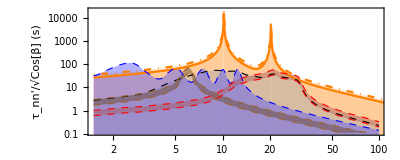

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\new_taubp_A-sidereal_pr_APS-90cl_3.png

```mathematica
exprt3d=LogLogPlot[
{
(*1*)ConditionalExpression[2.5,.8<bp<100],
(*2*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,mac1095o]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,mac2095o]^4)/2)^0.25,
(*3*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095o]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095o]^4)/2)^0.25,
(*4*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,mac1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,mac2095]^4)/2)^0.25,
(*5*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095]^4)/2)^0.25,
(*6*)ConditionalExpression[ftzbaglobal[bp],0.2<bp<100],
(*A*)
(*7*)ConditionalExpression[ftzba1[bp],0.2<bp<100],
(*8*)ConditionalExpression[ftzba2u[bp],0.2<bp<100],
(*9*)ConditionalExpression[ftzba2l[bp],0.2<bp<100],
(*10*)ConditionalExpression[ftzba3u[bp],0.2<bp<100],
(*11*)ConditionalExpression[ftzba3l[bp],0.2<bp<100]
},{bp,1.5,3000},
PlotRange->{{1.5,99},{.11,20499}},Axes->None,GridLines->Automatic,
Filling->{
None,
None,
{3->{0.001,Directive[Opacity[.45],Lighter[Orange]]}},
None,
{5->{0.001,Directive[Opacity[.25],Lighter[Orange]]}},
{6->{0.001,Directive[Opacity[.45],Lighter[Gray]]}},
{7->{0.001,Directive[Opacity[.45],Lighter[Blue]]}},
{8->{{9},Directive[Opacity[.45],Darker[Brown]]}},
{10->{{11},Directive[Opacity[.45],Darker[Pink]]}}
},PlotStyle->{
None,
(*2*)None,
(*3*){Orange,Thickness[thk]},
(*4*)None,
(*5*){Orange,Thickness[thk],DotDashed},
(*6*){Black,Dashed,Thickness[thk/2]},
(*7*){Blue,Dashed,Thickness[thk/2]},
(*8*){Brown,Dashed,Thickness[thk/2]},
(*9*){Brown,Dashed,Thickness[thk/2]},
(*10*){Red,Dashed,Thickness[thk/2]},
(*11*){Red,Dashed,Thickness[thk/2]}
},Frame->True,FrameStyle->Thickness[thk],FrameTicks->{(*y,x*){tk22[-1,5,.02,0,0.015,0,1],tk22[-1,5,.02,0,0.015,0,1]},{tk3[-1,3,.02,0,0.015,0,1/4],tk22[-1,3,.02,0,0.015,0,1]}},FrameTicksStyle->{Directive[Black,Thickness[thk/2]],Directive[Black,Thickness[thk]]},FrameLabel->{"B' (μT)","τ_nn'/√Cos[β] (s)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},ImageSize->{1400},AspectRatio->1/2.5
]
Export[StringJoin[PicDir,seperator,"new_taubp_A-sidereal_pr_APS-90cl_3.png"],exprt3d]
```

InterpolatingFunction::dmval: Input value {110.497} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {110.285} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {110.289} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

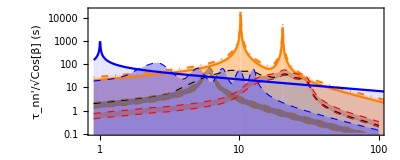

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\new_taubp_A-sidereal-nEDM.png

```mathematica
exprt3f=LogLogPlot[
{
(*1*)ConditionalExpression[2.5,.8<bp<100],
(*2*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,mac1095o]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,mac2095o]^4)/2)^0.25,
(*3*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095o]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095o]^4)/2)^0.25,
(*4*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,mac1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,mac2095]^4)/2)^0.25,
(*5*)((taubca[bp*10^(-6),(Mean[b10][[1]]-1.96Mean[b10][[2]])*0.001,ma1095]^4)/2+(taubca[bp*10^(-6),(Mean[b20][[1]]-1.96Mean[b20][[2]])*0.001,ma2095]^4)/2)^0.25,
(*6*)ConditionalExpression[ftzbaglobal[bp],0.2<bp<100],
(*A*)
(*7*)ConditionalExpression[ftzba1[bp],0.2<bp<100],
(*8*)ConditionalExpression[ftzba2u[bp],0.2<bp<100],
(*9*)ConditionalExpression[ftzba2l[bp],0.2<bp<100],
(*10*)ConditionalExpression[ftzba3u[bp],0.2<bp<100],
(*11*)ConditionalExpression[ftzba3l[bp],0.2<bp<100],
(*12*)((taubr[bp*10^(-6),10^(-6),gamman95*Sqrt[1/(1.96*wrasym[[2]])]]^4))^0.25
},{bp,.9,3000},
PlotRange->{{.9,99},{.11,20499}},Axes->None,GridLines->Automatic,
Filling->{
None,
None,
{3->{0.001,Directive[Opacity[.45],Lighter[Orange]]}},
None,
{5->{0.001,Directive[Opacity[.25],Lighter[Orange]]}},
{6->{0.001,Directive[Opacity[.45],Lighter[Gray]]}},
{7->{0.001,Directive[Opacity[.45],Lighter[Blue]]}},
{8->{{9},Directive[Opacity[.45],Darker[Brown]]}},
{10->{{11},Directive[Opacity[.45],Darker[Pink]]}},
{12->{0.001,Directive[Opacity[.15],Lighter[Blue]]}}
},PlotStyle->{
None,
(*2*)None,
(*3*){Orange,Thickness[thk]},
(*4*)None,
(*5*){Orange,Thickness[thk],DotDashed},
(*6*){Black,Dashed,Thickness[thk/2]},
(*7*){Blue,Dashed,Thickness[thk/2]},
(*8*){Brown,Dashed,Thickness[thk/2]},
(*9*){Brown,Dashed,Thickness[thk/2]},
(*10*){Red,Dashed,Thickness[thk/2]},
(*11*){Red,Dashed,Thickness[thk/2]},
(*12*){Blue,Thickness[thk]}
},Frame->True,FrameStyle->Thickness[thk],FrameTicks->{(*y,x*){tk22[-1,5,.02,0,0.015,0,1],tk22[-1,5,.02,0,0.015,0,1]},{tk3[-1,3,.02,0,0.015,0,1/4],tk22[-1,3,.02,0,0.015,0,1]}},FrameTicksStyle->{Directive[Black,Thickness[thk/2]],Directive[Black,Thickness[thk]]},FrameLabel->{"B' (μT)","τ_nn'/√Cos[β] (s)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},ImageSize->{1400},AspectRatio->1/2.5
]
Export[StringJoin[PicDir,seperator,"new_taubp_A-sidereal-nEDM.png"],exprt3f]
```